## Exercises: Random Variables

#### 1. Joey manipulates a die to increase his chances of winning a board game against his friends. In each round, a die is rolled and larger numbers are generally an advantage. Consider the random variable X denoting the outcome of the rolled die and the respective probabilities P(X = 1 = 2 = 3 = 5) = 1/9, P(X = 4) = 2/9, and P(X = 6) = 3/9. (a) Calculate and interpret the expectation and variance of X. (b) Imagine that the board game contains an action which makes the players use 1/X rather than X. What is the expectation of Y = 1/X? Is E(Y ) = E(1/X) =1/(E(X))?

(a) The probability mass function of X is
-Graphics-
The expectation is equal to:
E(X)=(1/9) 1+(1/9)2+(1/9)3+(2/9)4+(1/9)5+(3/9)6=37/9  which is approximately equal to 4.1.

To calculate the variance, we first need:
E(X^2)=(1/9) 1+(1/9)4+(1/9)9+(2/9)16+(1/9)25+(3/9)36=179/9  .
Using Var(X)=E(X^2)-(E(X))^2=(179/9)-(37/9)^2=242/81 which is approximately equal to 2.98.

The manipulated die yields on average higher values than a fair die because its expectation is 4.1 > 3.5. The variability of is, however, similar because 2.98 ≈2.92.

(b) The probability mass function of Y = 1/X is:
-Graphics-
The expectation value is then calculated as:
E(1/X)=(1/9) 1+(1/9)(1/2)+(1/9)(1/3)+(2/9)(1/4)+(1/9)(1/5)+(3/9)(1/6)=91/270

```mathematica
91./270.
```

0.337037

Let’s check whether E(1/X) is equal to 1/E(X):

```mathematica
1./(37./9.)
```

0.243243

This shows clearly that  that E(1/X) is different from 1/(E(X)). Recall that E(bX) = bE(X). It is interesting to see that for some transformations T(X) it holds that E(T(X)) = T(E(X)), but for some it does not. This reminds us to
be careful when thinking of the implications of transformations.

#### 2. An innovative winemaker experiments with new grapes and adds a new wine to his stock. The percentage sold by the end of the season depends on the weather and various other factors. It can be modelled using the random variable X with the CDF as -Graphics- (a) Plot the cumulative distribution function with Mathematica. (b) Determine the probability density function f (x). (c) What is the probability of selling at least one-third of his wine, but not more than two thirds? (try to calculate this with pen and paper). (d) Calculate the probability of (c) again using Mathematica. (e) What is the variance of X?

```mathematica
F[x_]:=Piecewise[{{0,x<0},{3*x^2-2*x^3,0<=x<=1},{1,x>1}}]
```

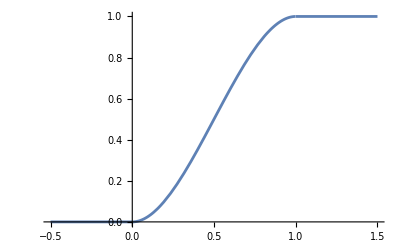

```mathematica
Plot[F[x],{x,-0.5,1.5}]
```

(d) The solution using the function F(x) defined above is:

```mathematica
F[2./3.]-F[1./3.]
```

0.481481

(e) The variance of X, using pen and paper, is:

You can do this also with Mathematica as follows:

```mathematica
f[x_]:=6*(x-x^2)
```

```mathematica
expvaluex=Integrate[x*f[x],{x,0,1}]
```

1/2

```mathematica
expvaluex2=Integrate[x^2*f[x],{x,0,1}]
```

3/10

```mathematica
var=expvaluex2-(expvaluex)^2
```

1/20

```mathematica
N[var]
```

0.05

#### 3. Consider the joint PDF for the type of customer service X (0 =telephonic hotline, 1 = Email) and of satisfaction score Y (1 = unsatisfied, 2 = satisfied, 3 = very satisfied): -Graphics- (a) Determine and interpret the marginal distributions of both X and Y . (b) Calculate the 75 % quantile for the marginal distribution of Y . (c) Determine and interpret the conditional distribution of satisfaction level for X =1. (d) Are the two variables independent? (e) Calculate and interpret the covariance of X and Y .